```mathematica
Zip[a_,b_]:=MapIndexed[({#1,b[[First[#2]]]})&,a];
```

```mathematica
ShowMultiGraph[Uk_, styles_]:=Module[
{edges},
styleSet[s_] := (Style[#,s[[2]]])&/@s[[1]];
edges = Catenate[ styleSet/@Zip[Uk,styles]];
Return[Graph[edges]];
];
```

{{1->2,2->3},{3->1}}

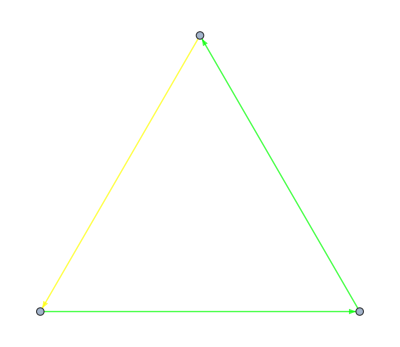

```mathematica
S={{1->2,2->3 },{3->1 }}
ShowMultiGraph[S,{Green,Yellow}]
```